# Muon Production in SM - e^-e^+-> μ^- μ^+

## Load FeynArts and FormCalc

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
<<"/home/riccardo/Programs/FormCalc/FormCalc-9.10/FormCalc.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Quit[]
```

## Set-up

```mathematica
CKM=IndexDelta;
```

```mathematica
process={V[1]} -> {F[2,{2}], -F[2,{2}]};
```

```mathematica
name="A-mm-SM";
```

```mathematica
SetOptions[InsertFields,Model->"SM",InsertionLevel->Particles];
SetOptions[Paint,PaintLevel->{Classes},ColumnsXRows->{4,5}];
```

## Tree-Level

## Topologies

> Top. 1 ad/bdcd/0.m, 0 diagrams

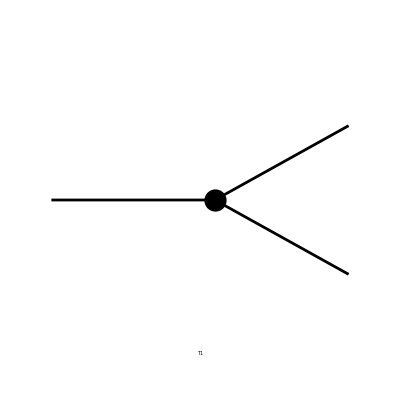

```mathematica
tops=CreateTopologies[0,1->2,Adjacencies->3];
Paint[tops];
```

## Insertions

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

in total: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 1 ad/bdcd/0.m, 0 diagrams

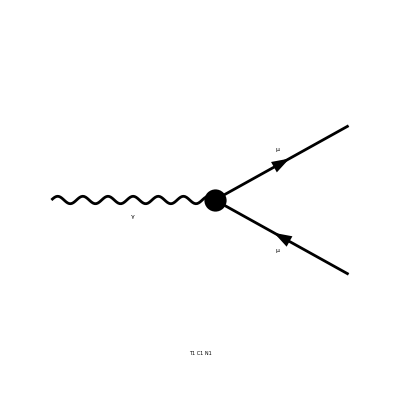

```mathematica
ins=InsertFields[tops, process];
Paint[ins];
```

## Feynman Amplitudes

```mathematica
amp=CreateFeynAmp[ins,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[],ⅈ ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] ep[V[1],p1,Lor1]]]

## FormCalc results

```mathematica
result=CalcFeynAmp[amp]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-EL (F1+F2)]

## One-Loop

## Topologies

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

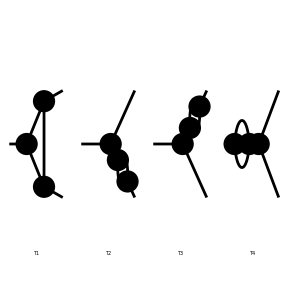

```mathematica
tops1=CreateTopologies[1,1->2,Adjacencies->3,ExcludeTopologies->Tadpoles];
Paint[tops1];
```

## Insertions

Excluding 2 Generic, 21 Classes, and 25 Particles fields

inserting at level(s) {Generic,Classes,Particles}

> Top. 1: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 2: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 3: 1 Generic, 1 Classes, 1 Particles insertions

> Top. 4: 1 Generic, 3 Classes, 9 Particles insertions

Restoring 2 Generic, 21 Classes, and 25 Particles fields

in total: 4 Generic, 6 Classes, 12 Particles insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

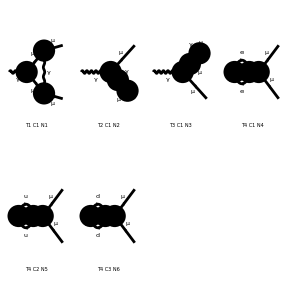

```mathematica
ins1=InsertFields[tops1, process,QEDOnly];
Paint[ins1, PaintLevel->{Classes}];
```

## Feynman Amplitudes

```mathematica
amp1=CreateFeynAmp[ins1,AmplitudeLevel->{Particles}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 9 Particles amplitudes

in total: 12 Particles amplitudes

FeynAmpList[Process→{{V[1],p1,0,{}}}→{{F[2,{2}],k1,MM,{-Charge,LeptonNumber}},{-F[2,{2}],k2,MM,{Charge,-LeptonNumber}}},Model→{SM},GenericModel→{Lorentz},AmplitudeLevel→{Particles},ExcludeParticles→{S,-F[1],F[1],-F[1,{1}],F[1,{1}],-F[1,{2}],F[1,{2}],-F[1,{3}],F[1,{3}],Mix[S,V],S[1],S[2],-S[3],S[3],-U[2],U[2],-U[3],U[3],-U[4],U[4],V[2],-V[3],V[3],Mix[S,V][2],-Mix[S,V][3],Mix[S,V][3],Rev[S,V][2],-Rev[S,V][3],Rev[S,V][3]},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1,Particles==1,Number==1],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).(MM+gs[q1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[q1-k1-k2]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1-k1)^2,1/(-MM2+(q1-k1-k2)^2)] g[Lor2,Lor3] ep[V[1],p1,Lor1]],FeynAmp[GraphID[Topology==2,Generic==1,Particles==1,Number==2],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).(MM+gs[-(k2)]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).(MM+gs[q1]).(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1+k2)^2] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-MM2+(k2)^2)],FeynAmp[GraphID[Topology==3,Generic==1,Particles==1,Number==3],Integral[q1],-1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).(MM+gs[-(q1)]).(ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+).(MM+gs[k1]).(ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(q1+k1)^2] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-MM2+(k1)^2)],FeynAmp[GraphID[Topology==4,Generic==1,Particles==1,Number==4],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-ME2+(q1)^2),1/(-ME2+(q1-k1-k2)^2)] tr[ME+gs[-(q1)],ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+,ME+gs[-(q1)+k1+k2],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2],FeynAmp[GraphID[Topology==4,Generic==1,Particles==2,Number==5],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MM2+(q1)^2),1/(-MM2+(q1-k1-k2)^2)] tr[MM+gs[-(q1)],ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+,MM+gs[-(q1)+k1+k2],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2],FeynAmp[GraphID[Topology==4,Generic==1,Particles==3,Number==6],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-ML2+(q1)^2),1/(-ML2+(q1-k1-k2)^2)] tr[ML+gs[-(q1)],ⅈ EL ga[Lor3].om_-+ⅈ EL ga[Lor3].om_+,ML+gs[-(q1)+k1+k2],ⅈ EL ga[Lor1].om_-+ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2],FeynAmp[GraphID[Topology==4,Generic==1,Particles==4,Number==7],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MU2+(q1)^2),1/(-MU2+(q1-k1-k2)^2)] tr[MU+gs[-(q1)],-2/3 ⅈ EL ga[Lor3].om_--2/3 ⅈ EL ga[Lor3].om_+,MU+gs[-(q1)+k1+k2],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]],FeynAmp[GraphID[Topology==4,Generic==1,Particles==5,Number==8],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MC2+(q1)^2),1/(-MC2+(q1-k1-k2)^2)] tr[MC+gs[-(q1)],-2/3 ⅈ EL ga[Lor3].om_--2/3 ⅈ EL ga[Lor3].om_+,MC+gs[-(q1)+k1+k2],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]],FeynAmp[GraphID[Topology==4,Generic==1,Particles==6,Number==9],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MT2+(q1)^2),1/(-MT2+(q1-k1-k2)^2)] tr[MT+gs[-(q1)],-2/3 ⅈ EL ga[Lor3].om_--2/3 ⅈ EL ga[Lor3].om_+,MT+gs[-(q1)+k1+k2],-2/3 ⅈ EL ga[Lor1].om_--2/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]],FeynAmp[GraphID[Topology==4,Generic==1,Particles==7,Number==10],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MD2+(q1)^2),1/(-MD2+(q1-k1-k2)^2)] tr[MD+gs[-(q1)],1/3 ⅈ EL ga[Lor3].om_-+1/3 ⅈ EL ga[Lor3].om_+,MD+gs[-(q1)+k1+k2],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]],FeynAmp[GraphID[Topology==4,Generic==1,Particles==8,Number==11],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MS2+(q1)^2),1/(-MS2+(q1-k1-k2)^2)] tr[MS+gs[-(q1)],1/3 ⅈ EL ga[Lor3].om_-+1/3 ⅈ EL ga[Lor3].om_+,MS+gs[-(q1)+k1+k2],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]],FeynAmp[GraphID[Topology==4,Generic==1,Particles==9,Number==12],Integral[q1],1/(16 π^4)ū[k1,MM].(ⅈ EL ga[Lor2].om_-+ⅈ EL ga[Lor2].om_+).v[k2,MM] FeynAmpDenominator[1/(-MB2+(q1)^2),1/(-MB2+(q1-k1-k2)^2)] tr[MB+gs[-(q1)],1/3 ⅈ EL ga[Lor3].om_-+1/3 ⅈ EL ga[Lor3].om_+,MB+gs[-(q1)+k1+k2],1/3 ⅈ EL ga[Lor1].om_-+1/3 ⅈ EL ga[Lor1].om_+] g[Lor2,Lor3] ep[V[1],p1,Lor1] 1/(-(k1)-k2)^2 SumOver[Col4,3]]]

## FormCalc results

```mathematica
result1=CalcFeynAmp[amp1]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][1/π Alfa EL (-Sub1 (C0i[cc1,MM2,0,MM2,0,MM2,MM2]+C0i[cc2,MM2,0,MM2,0,MM2,MM2])+(F3+F4) MM Pair1 (C0i[cc11,MM2,0,MM2,0,MM2,MM2]+2 C0i[cc12,MM2,0,MM2,0,MM2,MM2]+C0i[cc22,MM2,0,MM2,0,MM2,MM2])+(F1+F2) (Finite/4-1/2 B0i[bb0,MM2,0,MM2]+C0i[cc00,MM2,0,MM2,0,MM2,MM2]+(A0[ME2]+A0[ML2]+A0[MM2]+1/3 (A0[MB2]+A0[MD2]+A0[MS2])+4/3 (A0[MC2]+A0[MT2]+A0[MU2])-2 (B0i[bb00,0,ME2,ME2]+B0i[bb00,0,ML2,ML2]+B0i[bb00,0,MM2,MM2])-2/3 (B0i[bb00,0,MB2,MB2]+B0i[bb00,0,MD2,MD2]+B0i[bb00,0,MS2,MS2])-8/3 (B0i[bb00,0,MC2,MC2]+B0i[bb00,0,MT2,MT2]+B0i[bb00,0,MU2,MU2])) Den[0,0]+MM2 (-C0i[cc0,MM2,0,MM2,0,MM2,MM2]+(Finite-2 B0i[bb0,MM2,0,MM2]+2 B0i[bb1,MM2,0,MM2]) Den[MM2,MM2])))]

## Amplitude manipulations

## Amplitude manipulation tools

```mathematica
calcFeynAmp[amp_,i_Integer/;i≥0]:=CalcFeynAmp[amp[[0]][amp[[i]]]]
```

```mathematica
calcFeynAmpList[amp_]:=Map[CalcFeynAmp[amp[[0]][#]]&,amp]/.amp[[0]]->List
```

## Computations

```mathematica
Length[amp1]
```

12

```mathematica
result1List=calcFeynAmpList[amp1];
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

```mathematica
uvDiv=Map[UVDivergentPart,result1List]
```

{Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa Divergence EL (F1+F2))/(4 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π)],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0],Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][0]}

```mathematica
uvDiv=Map[#[[1]]&,uvDiv]
```

{-(Alfa Divergence EL (F1+F2))/(4 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),-(3 Alfa Divergence EL (F1+F2) MM2 Den[MM2,MM2])/(2 π),0,0,0,0,0,0,0,0,0}

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

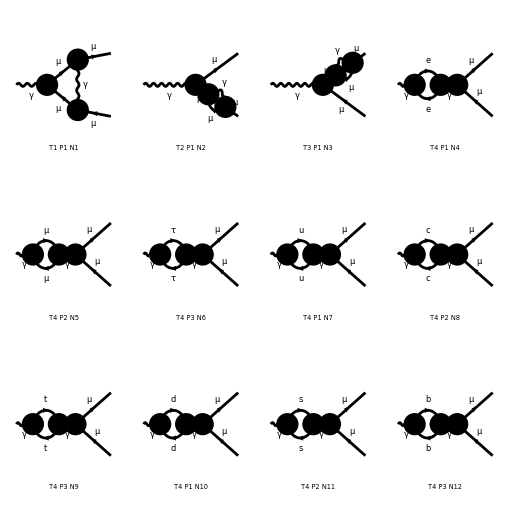

```mathematica
Paint[ins1,PaintLevel->{Particles},ColumnsXRows->{4,3}];
```

```mathematica
UVDivergentPart[result1]//Simplify
```

Amp[{{V[1],k[1],0,{}}}→{{F[2,{2}],k[2],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[3],MM,{Charge,-LeptonNumber}}}][-(Alfa EL (F1+F2) (Divergence+12 Divergence MM2 Den[MM2,MM2]))/(4 π)]

```mathematica
UVDivergentPart[calcFeynAmp[amp1,4]]
```

preparing FORM code in /home/riccardo/fc-amp-2.frm

running FORM...

ok

0